```mathematica
(*The following code is an example of how to implement the Explicit and Implicit methods to determine the UV Critical Surface of a QFT that is Asymptotically Safe, and how to make predictions of the complete couplings as functions of the relevant ones.*)
(*The example is based on a truncation up to ϕ^4 of a 2D scalar field theory, using the Local Potential Approximation, in a flat euclidean background*)
```

## Dimensionless Flow Equation - 2D Scalar Field in Euclidean flat background

```mathematica
vd[d_]:=1/(2(4Pi)^(d/2)Gamma[d/2]);
FlowEq[d_,U_,ϕ_,t_]:=D[U[t,ϕ],t]+ d*U[t,ϕ]-(d-2)/2 ϕ D[U[t,ϕ],ϕ]-(4vd[d])/d 1/(1+D[U[t,ϕ],ϕ,ϕ]);

LaurentCoefficientList[lpol_,x_]:=With[{min=Exponent[lpol,x,Min]},CoefficientList[lpol/x^min,x]];

evaluateVariables[expr_,vars_List,points_List]:=expr/. Thread[vars->points];
```

## Beta Functions, Fixed Points, Critical Exponents - 2 dimensional theory space truncation

```mathematica
Utest[t_,ϕ_]:=(Subscript[u, 0][t])/(Subscript[u, 4][t])+(Subscript[u, 2][t])/(2 Subscript[u, 4][t])ϕ^2+1/(4!Subscript[u, 4][t])ϕ^4;
NN=4;
UReplacements=Table[D[U[t,ϕ],{t,i},{ϕ,j}] -> D[Utest[t,ϕ],{t,i},{ϕ,j}],{i,0,1},{j,0,NN}]/.ϕ->0//Flatten;
TUReplacements=Table[D[U[t,ϕ],{t,i},{ϕ,j}] -> 0,{i,0,1},{j,NN+1,NN+5}]/.ϕ->0//Flatten;

CoefficientsEachPowerϕ=LaurentCoefficientList[Evaluate[Normal[Series[Evaluate[FlowEq[2,U,ϕ,t]],{ϕ,0,NN}]]/.UReplacements/.TUReplacements],ϕ]//FullSimplify;
```

```mathematica
(*For simplicity in the notation of the code, we define Subscript[u, 4][t]:=x and Subscript[u, 2][t]:=y*)
```

```mathematica
{Betay,Betax}=Values@Solve[{CoefficientsEachPowerϕ[[3]]==0,CoefficientsEachPowerϕ[[5]]==0},{Subscript[u, 2]'[t],Subscript[u, 4]'[t]}][[1]]/.Subscript[u, 4][t]->x/.Subscript[u, 2][t]->y/.ϵ->0/.d->2//FullSimplify
```

{-(x^2 (x+7 y))/(4 π (x+y)^3),2 x-(3 x^3)/(2 π (x+y)^3)}

```mathematica
(*Fixed Point Values*)
```

```mathematica
fp=Solve[{Betax==0,Betay==0}][[2]]
FP=Values@fp;
```

{x→343/(288 π),y→-49/(288 π)}

```mathematica
(*Critical Exponents*)
```

```mathematica
CE=-Eigenvalues[{{D[Betax,x],D[Betay,x]},{D[Betax,y],D[Betay,y]}}]/.x->FP[[1]]/.y->FP[[2]]//FullSimplify
```

{1/3 (-1+√43),1/3 (-1-√43)}

## Explicit Method for computing the UV Critical Hypersurface

```mathematica
(*The initial conditions of the explicit method are determined by the possible solutions of the CH using the linearized beta functions. In this case this means, that a first order expansion will give us the possible initial slopes of the CH for the 2D Scalar field*)
```

```mathematica
mslopesFP=Values@Solve[D[Normal[Series[(Betax/.y->y[x])D[y[x],x]-(Betay/.y->y[x]),{x,FP[[1]],1}]]/.y[FP[[1]]]->FP[[2]],x]==0];
```

```mathematica
(*Expansion of the CH from the NGFP*)
(*Not efficient but sufficient for obtaining the expansion*)
(*one solution for each initial slope of the CH - This might take 1 or 3 minutes to run*)
s1=AsymptoticDSolveValue[{(Betax/.y->y[x])D[y[x],x]-(Betay/.y->y[x])==0,y[FP[[1]]]==FP[[2]],y'[FP[[1]]]==mslopesFP[[1]][[1]]},y[x],{x,FP[[1]],10}];
s2=AsymptoticDSolveValue[{(Betax/.y->y[x])D[y[x],x]-(Betay/.y->y[x])==0,y[FP[[1]]]==FP[[2]],y'[FP[[1]]]==mslopesFP[[2]][[1]]},y[x],{x,FP[[1]],10}];
```

```mathematica
(*Plot of the obtained CH in the finite region of interest*)
```

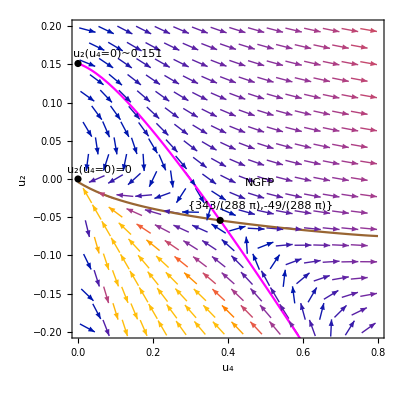

```mathematica
MaxY=2/10;
MinY=-2/10;

MaxX=8/10;
MinX=0;
Show[VectorPlot[{Betax,Betay},{x,MinX,MaxX},{y,MinY,MaxY}],Plot[Evaluate[(s1)//Normal],{x,MinX,MaxX},PlotStyle->Magenta],Plot[Evaluate[(s2)//Normal],{x,MinX,MaxX},PlotStyle->Brown],ListPlot[{FP,{0,0},{0,0.15107261413942966}},PlotStyle->Black],Epilog->{Black,Text["NGFP",Offset[{40,37},FP]],Text["{343/(288 π),-49/(288 π)}",Offset[{40,15},FP]],Text["u_2(u_4=0)=0",Offset[{21,10},{0,0}]],Text["u_2(u_4=0)~0.151",Offset[{40,10},{0,0.15107261413942966}]]},AxesLabel->{"u_4","u_2"},FrameLabel->{"u_4","u_2"},Background->White]
```

## Implicit Method for computing the UV Critical Hypersurface

-Graphics3D-

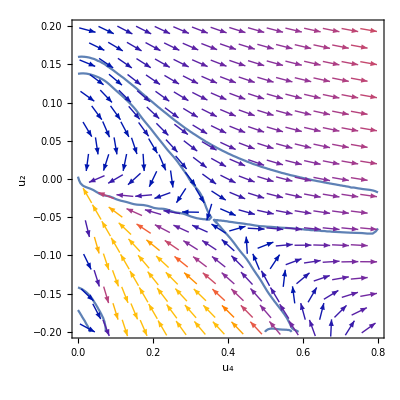

```mathematica
(*The equation for the generating function, in the case of a single irrelevant coupling, reduces to the following equation =0*)
CHFlowEq=((Betax)*D[F[x,y],x]+(Betay)*D[F[x,y],y]);

(*COMPACT DOMAIN TO STUDY*)

MaxY=2/10;
MinY=-2/10;

MaxX=8/10;
MinX=0;


(*Separation of the points in the square lattice used*)
DeltaX=0.025;
DeltaY=0.025;


(*Point that is forced to be contained in the lattice, in this case the NGFP, such that later we can make F exactly =0 at this point. Furthermore, the equation of the generating funtion is automatically satisfied at this point since all the beta functions are 0*)
StartPoint=FP;

(*Number of lattice points in each direction around the NGFP*)
NXD=Abs[(MinX-StartPoint[[1]])/DeltaX]//IntegerPart;
NXU=Abs[(MaxX-StartPoint[[1]])/DeltaX]//IntegerPart;
NYD=Abs[(MinY-StartPoint[[2]])/DeltaY]//IntegerPart;
NYU=Abs[(MaxY-StartPoint[[2]])/DeltaY]//IntegerPart;

(*Total number of points in the square lattice*)
NX=NXD+NXU+1;
NY=NYD+NYU+1;

(*Construction of the grid of points*)
SquareGrid=Table[{StartPoint[[1]]+ DeltaX*i,StartPoint[[2]]+ DeltaY*j},{i,-NXD,NXU},{j,-NYD,NYU}];


(*Construction of the approximating function, the parameters Subscript[f, i,j] are free*)
(*Spread of the approximating function*)
Sigma=5.3*DeltaX;ApproxGeneratingFunction=Sum[Sum[Subscript[f, i,j] 1/(1+((x-SquareGrid[[i+1]][[j+1]][[1]])^2+(y-SquareGrid[[i+1]][[j+1]][[2]])^2)/(2*Sigma^2)),{i,0,NX-1}],{j,0,NY-1}];
DXApproxGeneratingFunction=Sum[Sum[Subscript[f, i,j](-(x-SquareGrid[[i+1]][[j+1]][[1]]))/(Sigma^2 (1+((x-SquareGrid[[i+1]][[j+1]][[1]])^2+(y-SquareGrid[[i+1]][[j+1]][[2]])^2)/(2 Sigma^2))^2),{i,0,NX-1}],{j,0,NY-1}];
DYApproxGeneratingFunction=Sum[Sum[Subscript[f, i,j](-(y-SquareGrid[[i+1]][[j+1]][[2]]))/(Sigma^2 (1+((x-SquareGrid[[i+1]][[j+1]][[1]])^2+(y-SquareGrid[[i+1]][[j+1]][[2]])^2)/(2 Sigma^2))^2),{i,0,NX-1}],{j,0,NY-1}];



(*Points used to make one of the Subscript[f, i,j] different from 0 to avoid a trivial solution*)
PointSeeds=Nearest[Flatten[SquareGrid,1],StartPoint];


NonZeroPoint={SquareGrid[[NX]][[NY]][[1]],SquareGrid[[NX]][[NY]][[2]]};

NonZeroPoint={SquareGrid[[1]][[1]][[1]],SquareGrid[[1]][[1]][[2]]};

AppendTo[PointSeeds,NonZeroPoint];


IndexPointSeeds={};
IndexNonZeroPoint={};
For[i=1,i<=NX,i++,For[j=1,j<=NY,j++,If[MemberQ[PointSeeds,SquareGrid[[i]][[j]]],AppendTo[IndexPointSeeds,{i,j}],0]]];
For[i=1,i<=NX,i++,For[j=1,j<=NY,j++,If[SquareGrid[[i]][[j]]==NonZeroPoint,AppendTo[IndexNonZeroPoint,{i,j}],0]]];

IndexNonZeroPoint=Flatten[IndexNonZeroPoint];

SetOfUndeterminedIndices=Flatten[Delete[Table[{i,j},{i,1,NX},{j,1,NY}],IndexPointSeeds],1];



(*Discretization of he generating function equation*)
DiscreteCHEq[i_,j_]:=((Betax)*DXApproxGeneratingFunction+(Betay)*DYApproxGeneratingFunction)/.x->SquareGrid[[i]][[j]][[1]]/.y->SquareGrid[[i]][[j]][[2]];



(*Construction of the system of equations*)

SetOfEquations=Table[DiscreteCHEq[index[[1]],index[[2]]],{index,SetOfUndeterminedIndices}];
(*This forces the generating function to contain the non gaussian fixed point. This can also be done after obtaining F, and simply substracting the value of F at this point*)
AppendTo[SetOfEquations,(ApproxGeneratingFunction/.x->StartPoint[[1]]/.y->StartPoint[[2]])];
(*This forces the solution to be non trivial, since we already force it to be 0 in another point, and here we are forcing it to be equal to 1 at a different point. This automatically avoids the trivial solution*)
AppendTo[SetOfEquations,((ApproxGeneratingFunction/.x->NonZeroPoint[[1]]/.y->NonZeroPoint[[2]])-1)];
SetOfEquations=SetOfEquations//Flatten;
SetOfVariables=Flatten[Table[Subscript[f, i,j],{i,0,NX-1},{j,0,NY-1}],1];
(*Construction of the system of algebraic equations. In this case is just a linear system*)
{ConstVectorSEQ,MatrixSEQ}=CoefficientArrays[SetOfEquations,SetOfVariables]//N;


Solutions=LinearSolve[MatrixSEQ,-ConstVectorSEQ];
(*Construction of the approximated generating function*)
ReplacedApproxGeneratingFunction=ApproxGeneratingFunction/.Table[SetOfVariables[[i]]->Solutions[[i]],{i,1,Length[Solutions]}];
(*Just in case the numerical solver is not very exact, here we enforce the function to be 0 at the NGFP. Adding constants to the generating functions can always be done, since the equation is invariant under constants shifts*)
ReplacedApproxGeneratingFunction=ReplacedApproxGeneratingFunction-(ReplacedApproxGeneratingFunction/.x->StartPoint[[1]]/.y->StartPoint[[2]]);
Plot3D[ReplacedApproxGeneratingFunction,{x,MinX,MaxX},{y,MinY,MaxY},AxesLabel->{"u_4","u_2","F[u_4,u_2]"},PlotRange->All,Exclusions->None]
Show[ContourPlot[ReplacedApproxGeneratingFunction==0,{x,MinX,MaxX},{y,MinY,MaxY},FrameLabel->{"u_4","u_2"}],VectorPlot[{Betax,Betay},{x,MinX,MaxX},{y,MinY,MaxY}]]
```

```mathematica
(*Comparison of the kernel of the generating function F and the expansions obtained *)
```

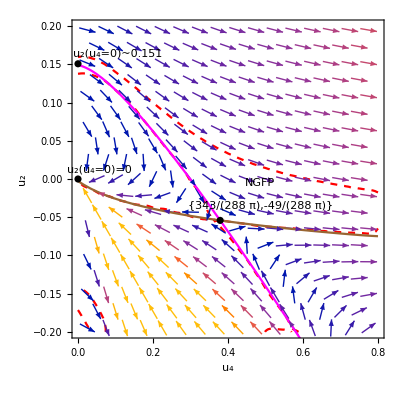

```mathematica
Show[ContourPlot[ReplacedApproxGeneratingFunction==0,{x,MinX,MaxX},{y,MinY,MaxY},ContourStyle->{Dashed,Red}],VectorPlot[{Betax,Betay},{x,MinX,MaxX},{y,MinY,MaxY}],Plot[Evaluate[s1],{x,MinX,MaxX},PlotStyle->Magenta],Plot[Evaluate[s2],{x,MinX,MaxX},PlotStyle->Brown],ListPlot[{FP,{0,0},{0,0.1507261413942966}},PlotStyle->Black],Epilog->{Black,Text["NGFP",Offset[{40,37},FP]],Text["{343/(288 π),-49/(288 π)}",Offset[{40,15},FP]],Text["u_2(u_4=0)=0",Offset[{21,10},{0,0}]],Text["u_2(u_4=0)~0.151",Offset[{40,10},{0,0.15107261413942966}]]},AxesLabel->{"u_4","u_2"},FrameLabel->{"u_4","u_2"},Background->White]
```